```mathematica
SetDirectory[NotebookDirectory[]];
Needs["MaTeX`"];
SetOptions[Charting`ScaledTicks,TicksLength->{.02,.01}];
```

## Decay, scattering and ratio in vacuum

```mathematica
Block[{CS,Cχdec,Cχscat,ratio},Row[{Print["Cχ decay=", Cχdec=(4Pi yχ^2)/(8Pi(2Pi)^3)mϕ^2(1-4 mχ^2/mϕ^2)^(3/2)Assuming[T>0&&mϕ>0,Integrate[√(Eϕ^2-mϕ^2)Exp[-Eϕ/T],{Eϕ,mϕ,Infinity}]]],
Print["Cχ decay expanded = ",Simplify[Cχdec/.mϕ->κ T/.BesselK[1,κ]->1/κ]],

Print["Cχ decay in massless limit = ",Simplify[Normal[Series[Cχdec/.mϕ->κ T/.BesselK[1,κ]->1/κ,{mχ,0,1}]]]],

Print["Cross section = ",CS=(yχ^2yψ^2)/(4Pi s)(1-(4mχ^2)/s)^(3/2)],

Print["Cχscat in massless limit = ",Cχscat=(2Pi^2 T)/(2Pi)^6 Assuming[T>0&&mχ>0&&yψ>0,Integrate[CS s^(3/2) BesselK[1,√s/T],{s,4mχ^2,Infinity}]]//Series[#,{mχ,0,3}]&//Normal//Simplify[#,T>0&&mχ>0]&],

Print["Cχscat/Cχdec = ",ratio=Simplify[Normal[Series[Cχscat/Cχdec/.mϕ->κ T/.BesselK[1,κ]->1/κ,{mχ,0,1}]]]],
 
Print["ratio = ", ratio/.κ->yψ/√6//N]}]]
```

Cχ decay=(mϕ^3 (1-(4 mχ^2)/mϕ^2)^(3/2) T yχ^2 1mϕ/T)/(16 π^3)

Cχ decay expanded = (T^4 yχ^2 (1-(4 mχ^2)/(T^2 κ^2))^(3/2) κ^2)/(16 π^3)

Cχ decay in massless limit = (T^4 yχ^2 κ^2)/(16 π^3)

Cross section = ((1-(4 mχ^2)/s)^(3/2) yχ^2 yψ^2)/(4 π s)

Cχscat in massless limit = (T^4 yχ^2 yψ^2)/(32 π^5)

Cχscat/Cχdec = yψ^2/(2 π^2 κ^2)

ratio = 0.303964

## Scattering with thermal propagator

### setup

```mathematica
gstar=106.75;
entropyS[T_]:=gstar (2Pi^2)/45 T^3;
Hubble[T_]:= 1.66(√gstar)/MPlanck T^2;

MPlanck=1.22 10^(19);

entropytoday=2891.2;

ρch2=1.05 10^(-5);

ReRϕ[T_,yψ_]:=yψ^2/6 T^2; 
kappa[yψ_?NumericQ]:=yψ/(√6);
ImRϕ[s_,yψ_]:=yψ^2/(8Pi)s;
```

### scattering rate--Boltzmann

```mathematica
(*factor out yχ^2*)

CSTdependent[T_?NumericQ,s_?NumericQ,mχ_?NumericQ,yψ_?NumericQ]:=yψ^2/(4Pi)(1-(4mχ^2)/s)^(3/2)s/((s-ReRϕ[T,yψ])^2+ImRϕ[s,yψ]^2);

(*define xs=s/T^2 and xχ=mχ/T; factor out yχ^2/T^2: *)
CSTindependent[xs_?NumericQ,xχ_?NumericQ,yψ_?NumericQ]:=yψ^2/(4Pi)(1-(4xχ^2)/xs)^(3/2)xs/((xs-yψ^2/6)^2+(xs yψ^2/(8Pi))^2) ;

CχscatTdependent[T_?NumericQ,mχ_?NumericQ,yψ_?NumericQ]:= (2Pi^2 T)/(2Pi)^6 NIntegrate[CSTdependent[T,s,mχ,yψ]s^(3/2) BesselK[1,√s/T],{s, 4mχ^2,Infinity},Exclusions->{s==ReRϕ[T,yψ]},MinRecursion->3];

(*factor out yχ^2 T^4: *)

CχscatTindependent[xχ_?NumericQ,yψ_?NumericQ]:= (2Pi^2)/(2Pi)^6 NIntegrate[CSTindependent[xs,xχ,yψ] xs^(3/2) BesselK[1,√xs],{xs, 4xχ^2,Infinity},Exclusions->{xs==yψ^2/6},MinRecursion->3];

(*factor out yχ^2/mχ due to the Planck mass in Hubble. So Yχscatint below is defined as dYscat/dxχ mχ/yχ^2   *)

dYχdxχscat[xχ_?NumericQ,yψ_?NumericQ]:=(*1/mχ*)(2CχscatTindependent[xχ,yψ]( 1/xχ)^4)/(entropyS[1/xχ] Hubble[1/xχ] (1/xχ))1/xχ^2; 

Yχscat[mχ_?NumericQ,yψ_?NumericQ]:=Assuming[mχ>0&&yψ>0,NIntegrate[(2CχscatTdependent[T,mχ,yψ])/(entropyS[T] Hubble[T] T) , {T,0,Infinity},MinRecursion->2]];

YχscatTR[TR_?NumericQ,mχ_?NumericQ,yψ_?NumericQ]:=Assuming[TR>0&&mχ>0&&yψ>0,NIntegrate[(2CχscatTdependent[T,mχ,yψ])/(entropyS[T] Hubble[T] T) , {T,0,TR},Method->"LocalAdaptive"]];

ωχscat[mχ_?NumericQ,yψ_?NumericQ]:=Yχscat[mχ,yψ] entropytoday/ρch2 mχ;
ωχscatTR[TR_?NumericQ,mχ_?NumericQ,yψ_?NumericQ]:=YχscatTR[TR,mχ,yψ] entropytoday/ρch2 mχ;

yχscatFit[mχ_?NumericQ,yψ_?NumericQ]:=√(0.12/ωχscat[mχ,yψ]);

yχscatFitTR[TR_?NumericQ,mχ_?NumericQ,yψ_?NumericQ]:=√(0.12/ωχscatTR[TR,mχ,yψ]);
```

### scattering rate-quantum statistics

```mathematica
(*define xs=s/T^2 and xχ=mχ/T; factor out yχ^2/T^2: *)
```

```mathematica
CSfull[xs_?NumericQ,xχ_?NumericQ,yψ_?NumericQ]:=yψ^2/(4Pi)(1-(4xχ^2)/xs)^(3/2)xs/((xs-yψ^2/6)^2+(xs yψ^2/(8Pi))^2);
CSVacfull[xs_?NumericQ,xχ_?NumericQ,yψ_?NumericQ]:=yψ^2/(4Pi)(1-(4xχ^2)/xs)^(3/2)1/xs;

CχscatVacfull[xχ_?NumericQ,yψ_?NumericQ]:=(2Pi^2)/(2Pi)^6 NIntegrate[CSVacfull[xs,xχ,yψ] xs/2 1/(Exp[(xE1+xE2)/2]+1)1/(Exp[(xE1-xE2)/2]+1)UnitStep[(xE1^2-xs)-xE2^2]UnitStep[xE1-√xs],{xE2,-Infinity,Infinity},{xE1,0,Infinity},{xs,4xχ^2,Infinity},MinRecursion->5,Method->{"MonteCarloRule"}];

(*factor out yχ^2 T^4: *)
Cχscatfull[xχ_?NumericQ,yψ_?NumericQ]:=(2Pi^2)/(2Pi)^6 NIntegrate[CSfull[xs,xχ,yψ] xs/2 1/(Exp[(xE1+xE2)/2]+1)1/(Exp[(xE1-xE2)/2]+1)UnitStep[(xE1^2-xs)-xE2^2]UnitStep[xE1-√xs],{xE2,-Infinity,Infinity},{xE1,0,Infinity},{xs,4xχ^2,Infinity},Exclusions->{xs==yψ^2/6},MinRecursion->10,MaxRecursion->20,Method->{"MonteCarloRule"}];

Yχscatfull[mχ_?NumericQ,yψ_?NumericQ]:=2(2Pi^2)/(2Pi)^6 NIntegrate[ CSfull[xs,xχ,yψ] xs/2 1/(Exp[(xE1+xE2)/2]+1)1/(Exp[(xE1-xE2)/2]+1)UnitStep[(xE1^2-xs)-xE2^2]UnitStep[xE1-√xs]UnitStep[xs-4xχ^2](mχ/xχ)^4/(entropyS[mχ/xχ] Hubble[mχ/xχ] mχ/xχ)mχ/xχ^2,{xE2,-Infinity,Infinity},{xE1,0,Infinity},{xs,0,Infinity}, {xχ,0,Infinity},Exclusions->{xs==yψ^2/6},MinRecursion->10,MaxRecursion->20,Method->{"MonteCarloRule"}];
ωχscatfull[mχ_?NumericQ,yψ_?NumericQ]:=Yχscatfull[mχ,yψ] entropytoday/ρch2 mχ;
```

```mathematica
(*check convergence of MC method*)
```

```mathematica
Do[Print[intnumMonteCarloelectron[i]=Cχscatfull[0.0001,0.01]]//AbsoluteTiming,{i,4}]

Do[Print[intnumMonteCarloelectron[i]=Yχscatfull[0.0001,0.01]]//AbsoluteTiming,{i,4}]
```

### decay rate-Boltzmann

```mathematica
mϕT[T_,yψ_]:=√ReRϕ[T,yψ];

Tc[mχ_,yψ_]:=2mχ/(yψ/√6);

Cχdec[T_,mχ_,yψ_]:=1/(16Pi^3)mϕT[T,yψ]^3(1-(4mχ^2)/mϕT[T,yψ]^2)^(3/2)T BesselK[1,mϕT[T,yψ]/T];
(* factor out yχ^2 T^4:  *)
CχdecTindependent[xχ_,yψ_]:=Cχdec[T,mχ,yψ]/T^4/.mχ->T xχ//Simplify[#,T>0]&;

Yχdec[mχ_?NumericQ,yψ_?NumericQ]:= Assuming[mχ>0&&yψ>0,NIntegrate[(2Cχdec[T,mχ,yψ])/(entropyS[T] Hubble[T] T) , {T,Tc[mχ,yψ],Infinity},MinRecursion->2]];

(*factor out yχ^2/mχ due to the Planck mass in Hubble. So dYχdxχdec below is defined as dYdec/dxχ mχ/yχ^2   *)

dYχdxχdec[xχ_?NumericQ,yψ_?NumericQ]:=(*1/mχ*)(2CχdecTindependent[xχ,yψ]( 1/xχ)^4)/(entropyS[1/xχ] Hubble[1/xχ] (1/xχ))1/xχ^2; 

YχdecTR[TR_?NumericQ,mχ_?NumericQ,yψ_?NumericQ]:=If[TR>Tc[mχ,yψ],Assuming[mχ>0&&yψ>0,NIntegrate[(2Cχdec[T,mχ,yψ])/(entropyS[T] Hubble[T] T), {T,Tc[mχ,yψ],TR},MinRecursion->2]],0];

ωχdec[mχ_?NumericQ,yψ_?NumericQ]:=Yχdec[mχ,yψ] entropytoday/ρch2 mχ;


ωχdecTR[TR_?NumericQ,mχ_?NumericQ,yψ_?NumericQ]:=YχdecTR[TR,mχ,yψ] entropytoday/ρch2 mχ;

yχdecFit[mχ_?NumericQ,yψ_?NumericQ]:=√(0.12/ωχdec[mχ,yψ]);

yχdecFitTR[TR_?NumericQ,mχ_?NumericQ,yψ_?NumericQ]:=If[TR>Tc[mχ,yψ],√(0.12/ωχdecTR[TR,mχ,yψ]),0];
```

### decay rate-quantum statistics

```mathematica
(* factor out yχ^2 T^4:  *)
```

```mathematica
Cχdecfull[xχ_?NumericQ,yψ_?NumericQ]:=(*T^4*)(4Pi (*yχ^2*))/(8Pi(2Pi)^3)kappa[yψ]^2(1-4 xχ^2/kappa[yψ]^2)^(3/2)NIntegrate[√(xE^2-kappa[yψ]^2)1/(Exp[xE]-1),{xE,kappa[yψ],Infinity}]; 

Yχdecfull[mχ_?NumericQ,yψ_?NumericQ]:= NIntegrate[(2Cχdecfull[xχ,yψ] (mχ/xχ)^4)/(entropyS[mχ/xχ] Hubble[mχ/xχ] mχ/xχ) mχ/xχ^2, {xχ,0,kappa[yψ]/2},MinRecursion->3];
ωχdecfull[mχ_?NumericQ,yψ_?NumericQ]:=Yχdecfull[mχ,yψ] entropytoday/ρch2 mχ;
```

### scat/decay ratio: collision rate

#### Ratio with Boltzmann distribution and vacuum scattering

```mathematica
CχdecVacBoltzmann=(4Pi yχ^2)/(8Pi(2Pi)^3)mϕ^2(1-4 mχ^2/mϕ^2)^(3/2)Assuming[T>0&&mϕ>0,Integrate[√(Eϕ^2-mϕ^2)Exp[-Eϕ/T],{Eϕ,mϕ,Infinity}]];
CχscatVacBoltzmann=(2Pi^2 T)/(2Pi)^6 Assuming[T>0&&mχ>0&&yψ>0,Integrate[(yχ^2yψ^2)/(4Pi s)(1-(4mχ^2)/s)^(3/2)  s^(3/2) BesselK[1,√s/T],{s,4mχ^2,Infinity}]]//Series[#,{mχ,0,3}]&//Normal//Simplify[#,T>0&&mχ>0]&;
RVacBoltzmann=Simplify[Normal[Series[CχscatVacBoltzmann/CχdecVacBoltzmann/.mϕ->κ T/.BesselK[1,κ]->1/κ,{mχ,0,1}]]]/.κ->yψ/√6//N
```

0.303964

#### Ratio with full distribution and vacuum scattering

```mathematica
RVacFD=Do[Print["γ_scat/γ_dec=",CχscatVacfull[10^-8,10^(-(5-i))]/Cχdecfull[10^-8,10^(-(5-i))]],{i,4}]
```

γ_scat/γ_dec=0.125042

γ_scat/γ_dec=0.125301

γ_scat/γ_dec=0.125472

γ_scat/γ_dec=0.129927

#### Ratio with Boltzmann distribution and thermally corrected scattering

```mathematica
RTBoltzmann=Do[Print["γ_scat/γ_dec=",CχscatTindependent[10^-8,10^(-(5-i))]/CχdecTindependent[10^-8,10^(-(5-i))]],{i,4}]
```

γ_scat/γ_dec=0.803964

γ_scat/γ_dec=0.803964

γ_scat/γ_dec=1.30401

γ_scat/γ_dec=1.30649

#### Ratio with full and thermally corrected scattering

```mathematica
RTFD=Do[Print["γ_scat/γ_dec=",Cχscatfull[10^-8,10^(-(5-i))]/Cχdecfull[10^-8,10^(-(5-i))]],{i,4}]
```

γ_scat/γ_dec=0.124602

γ_scat/γ_dec=0.125511

γ_scat/γ_dec=0.13475

γ_scat/γ_dec=0.235788

### scat v.s. decay--Boltzmann: plot

```mathematica
ScatDecPlot=LogLogPlot[{CχdecTindependent[xχ,0.1],CχscatTindependent[xχ,0.1],CχdecTindependent[xχ,0.01],CχscatTindependent[xχ,0.01],CχdecTindependent[xχ,0.001],CχscatTindependent[xχ,0.001],CχdecTindependent[xχ,0.0001],CχscatTindependent[xχ,0.0001]},{xχ,10^(-6),3},PlotRange->{{10^(-6),3},{10^-16,10^-4}},PlotStyle->{Directive[Darker@Green,Thickness[0.005]],Directive[Darker@Green,Dashing[Medium], Thickness[0.005]],Directive[RGBColor[0.3,0.56,1.],Thickness[0.005]],Directive[RGBColor[0.3,0.56,1.],Dashing[Medium], Thickness[0.005]],
Directive[Darker@Red,Thickness[0.005]],Directive[Darker@Red,Dashing[Medium],Thickness[0.005]],Directive[RGBColor[0.83,0.32,1.],Thickness[0.005]],Directive[RGBColor[0.83,0.32,1.],Dashing[Medium], Thickness[0.005]]},
GridLines->{{0.1/(2 √6),0.01/(2 √6),0.001/(2 √6),0.0001/(2 √6),(*xχ= *)√(1/4)},{}},GridLinesStyle->Directive[Black,Thickness[0.001],Dotted],
Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{MaTeX["\\boldsymbol{x_\\chi\\equiv m_\\chi/T}",FontSize->20],MaTeX["\\boldsymbol{\\gamma\\times y_\\chi^{-2}\\times T^{-4}}",FontSize->20]},
FrameTicksStyle->Directive[Black,Thickness[0.005],18],ImageSize->500,AspectRatio->0.75,Epilog->{Inset[LineLegend[{Directive[Black,Dashing[Medium]],Directive[Black]},{MaTeX["\\boldsymbol{\\textbf{scattering}}",FontSize->17],
MaTeX["\\boldsymbol{\\textbf{forbidden~decay}}",FontSize->17]},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Gray]&),LegendMargins->3,LegendLayout->{"Row",2}],Scaled[{0.75,0.16}]],
Inset[Rotate[Style[MaTeX["\\boldsymbol{y_\\psi=10^{-1}}",FontSize->17]],0Degree],Scaled[{0.15,0.92}]],
Inset[Rotate[Style[MaTeX["\\boldsymbol{y_\\psi=10^{-2}}",FontSize->17]],0Degree],Scaled[{0.15,0.76}]],
Inset[Rotate[Style[MaTeX["\\boldsymbol{y_\\psi=10^{-3}}",FontSize->17]],0Degree],Scaled[{0.15,0.6}]],
Inset[Rotate[Style[MaTeX["\\boldsymbol{y_\\psi=10^{-4}}",FontSize->17]],0Degree],Scaled[{0.15,0.42}]]
}]
```

-Graphics-

```mathematica
Export["collisionrate.pdf",Style[ScatDecPlot,Background->None]];
(*SystemOpen[DirectoryName[AbsoluteFileName["collisionrate.pdf"]]]*)
```

```mathematica
ScatDecPlot2=LogLogPlot[{dYχdxχdec[xχ,0.1],dYχdxχscat[xχ,0.1],dYχdxχdec[xχ,0.01],dYχdxχscat[xχ,0.01],dYχdxχdec[xχ,0.001],dYχdxχscat[xχ,0.001],dYχdxχdec[xχ,0.0001],dYχdxχscat[xχ,0.0001]},{xχ,10^(-6),3},PlotRange->{{10^(-6),3},{10^1,10^13}},PlotStyle->{Directive[Darker@Green,Thickness[0.005]],Directive[Darker@Green,Dashing[Medium], Thickness[0.005]],Directive[RGBColor[0.3,0.56,1.],Thickness[0.005]],Directive[RGBColor[0.3,0.56,1.],Dashing[Medium], Thickness[0.005]],
Directive[Darker@Red,Thickness[0.005]],Directive[Darker@Red,Dashing[Medium],Thickness[0.005]],Directive[RGBColor[0.83,0.32,1.],Thickness[0.005]],Directive[RGBColor[0.83,0.32,1.],Dashing[Medium], Thickness[0.005]]},
GridLines->{{0.1/(2 √6),0.01/(2 √6),0.001/(2 √6),0.0001/(2 √6),(*xχ= *)√(1/4)},{}},GridLinesStyle->Directive[Black,Thickness[0.001],Dotted],
Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{MaTeX["\\boldsymbol{x_\\chi\\equiv m_\\chi/T}",FontSize->20],MaTeX["\\boldsymbol{dY_\\chi/dx_\\chi\\times m_\\chi\\times y_\\chi^{-2} ~[\\textbf{GeV}]}",FontSize->20]},
FrameTicksStyle->Directive[Black,Thickness[0.005],18],ImageSize->500,AspectRatio->0.75,Epilog->{Inset[LineLegend[{Directive[Black,Dashing[Medium]],Directive[Black]},{MaTeX["\\boldsymbol{\\textbf{scattering}}",FontSize->17],
MaTeX["\\boldsymbol{\\textbf{forbidden~decay}}",FontSize->17]},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Gray]&),LegendMargins->3,LegendLayout->{"Row",2}],Scaled[{0.75,0.14}]],
Inset[Rotate[Style[MaTeX["\\boldsymbol{y_\\psi=10^{-1}}",FontSize->17]],0Degree],Scaled[{0.15,0.9}]],
Inset[Rotate[Style[MaTeX["\\boldsymbol{y_\\psi=10^{-2}}",FontSize->17]],0Degree],Scaled[{0.15,0.72}]],
Inset[Rotate[Style[MaTeX["\\boldsymbol{y_\\psi=10^{-3}}",FontSize->17]],0Degree],Scaled[{0.15,0.55}]],
Inset[Rotate[Style[MaTeX["\\boldsymbol{y_\\psi=10^{-4}}",FontSize->17]],0Degree],Scaled[{0.15,0.38}]]
}]
```

-Graphics-

```mathematica
Export["dYdx.pdf",Style[ScatDecPlot2,Background->None]];
```

### scat vs decay: relic density--Boltzmann+full quantum statistics

#### relic density ratio--Fit

```mathematica
OmegaRatio=Table[{yψ//N,ωχscat[1,yψ]/ωχdec[1,yψ]//N},{yψ,{10^(-5),(*3 10^(-5),*)5 10^(-5),(*7 10^(-5),*)1 10^(-4),5 10^(-4),(*6 10^(-4),9 10^(-4),*)1 10^(-3),5 10^(-3),(*7 10^(-3),9 10^(-3),*)0.01,(*0.02,0.03,*)0.05,(*0.06,0.08,*)0.1,(*0.2,0.3,0.4,*)0.5,(*0.6,0.7,0.8,0.9,*)1}}];
```

```mathematica
OmegaRatioFull=Table[{yψ//N,ωχscatfull[1,yψ]/ωχdecfull[1,yψ]//N},{yψ,{10^(-5),(*3 10^(-5),*)5 10^(-5),(*7 10^(-5),*)1 10^(-4),5 10^(-4),(*6 10^(-4),9 10^(-4),*)1 10^(-3),5 10^(-3),(*7 10^(-3),9 10^(-3),*)0.01,(*0.02,0.03,*)0.05,(*0.06,0.08,*)0.1,(*0.2,0.3,0.4,*)0.5,(*0.6,0.7,0.8,0.9,*)1}}];
```

```mathematica
OmegaRatioFit=FindFormula[OmegaRatio,yψ,5,All,TargetFunctions->{Times,Csc}, PerformanceGoal->"Quality", SpecificityGoal->Infinity]//Simplify
```

```mathematica
Table[{OmegaRatio[[i,2]]/OmegaRatioFull[[i,2]]},{i,1,5}]
```

(2.17478
2.20412
2.1862
2.17434
2.17177)

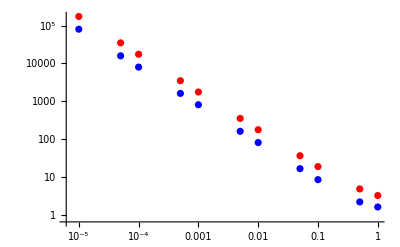

```mathematica
ListLogLogPlot[{OmegaRatio,OmegaRatioFull},PlotStyle->{Red,Blue}]
```

```mathematica
OmegaRatioFit=0.8 yψ+1.8/yψ+0.5;
OmegaRatioFullFit=OmegaRatioFit/2.2;
```

#### relic density ratio--plot

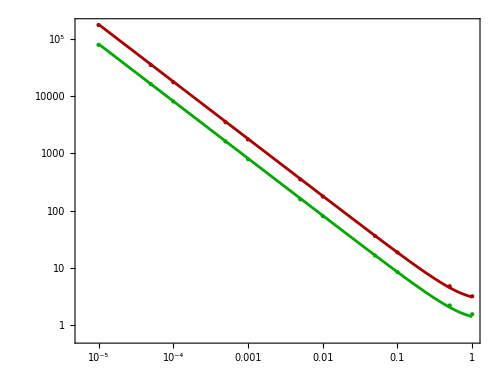

```mathematica
OmegaRatioPlot=Show[ListLogLogPlot[{OmegaRatio,OmegaRatioFull},PlotRange->All,PlotStyle->{Directive[Darker@Red,PointSize[Large]],Directive[Darker@Green,PointSize[Large]]}],LogLogPlot[{OmegaRatioFit,OmegaRatioFullFit},{yψ,10^(-5),1},PlotStyle->{Directive[Darker@Red,Thickness[0.004]],Directive[Darker@Green,Thickness@0.004]}],Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{MaTeX["\\boldsymbol{\\textbf{thermal~coupling}~y_\\psi}",FontSize->20],MaTeX["\\boldsymbol{\\Omega_{2\\psi\\to2\\chi,\\rm off }/\\Omega_{\\phi\\to 2\\chi}}",FontSize->20]},
FrameTicksStyle->Directive[Black,Thickness[0.005],18],ImageSize->500,AspectRatio->0.75,Epilog->{Inset[LineLegend[{Directive[Darker@Red],Directive[Darker@Green]},{MaTeX["\\boldsymbol{\\textbf{Boltzmann~Statistics}}",FontSize->17],
MaTeX["\\boldsymbol{\\textbf{Quantum Statistics}}",FontSize->17]},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Gray]&),LegendMargins->3,LegendLayout->{"Row",2}],Scaled[{0.72,0.85}]]}]
```

```mathematica
Export["OmegaR.pdf",Style[OmegaRatioPlot,Background->None]];
SystemOpen[DirectoryName[AbsoluteFileName["OmegaR.pdf"]]]
```

#### relic density--coupling correlation plot

```mathematica
ωχtot[yχ_?NumericQ,yψ0_?NumericQ]:=yχ^2(1+OmegaRatioFit/.yψ->yψ0)ωχdec[1,yψ0];
ωχFulltot[yχ_?NumericQ,yψ0_?NumericQ]:=yχ^2(1+OmegaRatioFullFit/.yψ->yψ0)ωχdecfull[1,yψ0];
```

```mathematica
{ωχdec[1,0.1]/ωχtot[1,0.1],ωχdec[1,1]/ωχtot[1,1],ωχdecfull[1,0.1]/ωχFulltot[1,0.1],ωχdecfull[1,1]/ωχFulltot[1,1]}
```

{0.0510725,0.243902,0.105871,0.415094}

```mathematica
Omegatot=ContourPlot[{ωχtot[yχ,yψ]==0.12,yχ^2 ωχdec[1,yψ]==0.12},{yψ,10^(-5),1},{yχ,5 10^-12,2 10^-4},ContourStyle->{Directive[RGBColor[1.,0.2,0.3],Thickness[0.005]],Directive[RGBColor[0.,0.15,0.7],Thickness@0.005]},ScalingFunctions->{"Log","Log"},Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],FrameLabel->{MaTeX["\\boldsymbol{\\textbf{thermal~coupling}~y_\\psi}",FontSize->20],MaTeX["\\boldsymbol{\\textbf{DM~coupling}~y_\\chi}",FontSize->20]},
FrameTicksStyle->Directive[Black,Thickness[0.005],18],ImageSize->500,AspectRatio->0.75];
```

```mathematica
Omegafulltot=ContourPlot[{ωχFulltot[yχ,yψ]==0.12,yχ^2 ωχdecfull[1,yψ]==0.12},{yψ,10^(-5),1},{yχ,5 10^-12,2 10^-4},ContourStyle->{Directive[RGBColor[1.,0.2,0.3],Thickness[0.005],Dashing[Large]],Directive[RGBColor[0.,0.15,0.7],Thickness@0.005,,Dashing[Large]]},ScalingFunctions->{"Log","Log"},Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{MaTeX["\\boldsymbol{\\textbf{thermal~coupling}~y_\\psi}",FontSize->20],MaTeX["\\boldsymbol{\\textbf{DM~coupling}~y_\\chi}",FontSize->20]},
FrameTicksStyle->Directive[Black,Thickness[0.005],18],ImageSize->500,AspectRatio->0.75];
```

```mathematica
Omegashow=Show[Omegatot,Omegafulltot,Epilog->{
Inset[Rotate[Style[MaTeX["\\boldsymbol{\\Omega_{\\rm scat+decay}=\\Omega_{\\rm obs}}",FontSize->17]],-26Degree],Scaled[{0.45,0.48}]],
Inset[Rotate[Style[MaTeX["\\boldsymbol{\\Omega_{\\rm decay}=\\Omega_{\\rm obs}}",FontSize->17]],-35Degree],Scaled[{0.5,0.62}]],
Inset[LineLegend[{Directive[Black],
Directive[Black,Dashing[Large]]},{MaTeX["\\boldsymbol{\\textbf{Boltzmann~Statistics}}",FontSize->15],
MaTeX["\\boldsymbol{\\textbf{Quantum~Statistics}}",FontSize->15]},LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Gray]&),LegendMargins->3,LegendLayout->{"Row",2}],Scaled[{0.72,0.85}]]}]
```

-Graphics-

```mathematica
Export["couplingco.pdf",Style[Omegashow,Background->None]];
(*SystemOpen[DirectoryName[AbsoluteFileName["couplingco.pdf"]]]*)
```